```mathematica
R1 = 1;
R2 = 0.5;
```

```mathematica
F1= 2 * ArcCos[(R1^2- R2^2 + d^2)/(2R1 d)];
F2= 2 * ArcCos[(R2^2- R1^2 + d^2)/(2R2 d)];
S1= R1^2 * (F1 - Sin@F1)/2;
S2= R2^2 * (F2 - Sin@F2)/2;
```

```mathematica
Scom = S1 + S2;
```

```mathematica
fun[d_] := 1/2 R1^2 (2 ArcCos[(d^2+R1^2-R2^2)/(2 d R1)]-Sin[2 ArcCos[(d^2+R1^2-R2^2)/(2 d R1)]])+1/2 R2^2 (2 ArcCos[(d^2-R1^2+R2^2)/(2 d R2)]-Sin[2 ArcCos[(d^2-R1^2+R2^2)/(2 d R2)]])
```

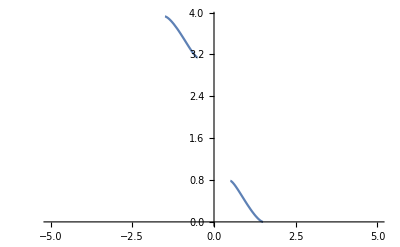

```mathematica
Plot[fun[d], {d, -5 ,5}]
```

```mathematica
InterArea[r1_, r2_, d_] := Piecewise[
{{1/2 r1^2 (2 ArcCos[(d^2+r1^2-r2^2)/(2 Abs@d r1)]-Sin[2 ArcCos[(d^2+r1^2-r2^2)/(2 Abs@d r1)]])+1/2 r2^2 (2 ArcCos[(d^2-r1^2+r2^2)/(2Abs@d r2)]-Sin[2 ArcCos[(d^2-r1^2+r2^2)/(2 Abs@d r2)]]), Abs@d ≤ (r1 + r2) && Abs@d ≥ Min[r1, r2]}, {Min[r1, r2]^2 * π,Abs@d≤Min[r1, r2]}}]
```

```mathematica
fun1[r1_, r2_, d_] := 1/2 r1^2 (2 ArcCos[(d^2+r1^2-r2^2)/(2d r1)]-Sin[2 ArcCos[(d^2+r1^2-r2^2)/(2d r1)]])+1/2 r2^2 (2 ArcCos[(d^2-r1^2+r2^2)/(2d r2)]-Sin[2 ArcCos[(d^2-r1^2+r2^2)/(2 d r2)]]);
```

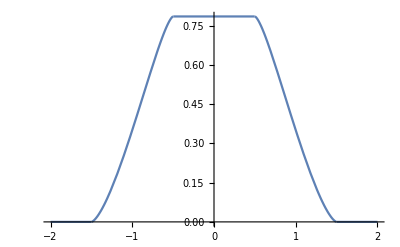

0.350767

```mathematica
Plot[InterArea[R1, R2, dis], {dis, -2, 2}]
InterArea[R1, R2, 1]//N
```